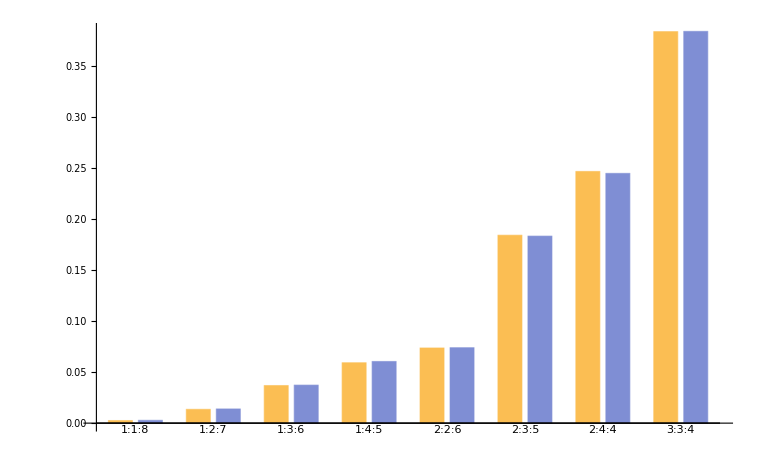

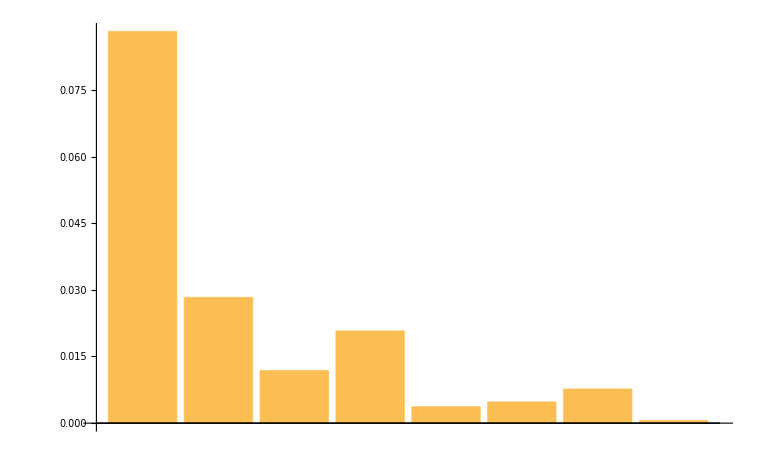

0.0120199

```mathematica
Statistical = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_20_statistical.csv"];
Statistical = Statistical[[;;,1]];
Analytical = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_20.csv"];
Analytical = Analytical[[;;,1]];

AnalyticalCounts = Sort[Counts[Analytical]];
NormalizedAnalyticalCounts = AnalyticalCounts/Total[AnalyticalCounts];

StatisticalCounts = Sort[Counts[Statistical]];
NormalizedStatisticalCounts = StatisticalCounts/Total[StatisticalCounts];

CombinedData = Association[Table[key -> {NormalizedAnalyticalCounts[key],NormalizedStatisticalCounts[key]},{key,Keys[NormalizedAnalyticalCounts]}]];

BarChart[CombinedData,ChartLabels->{Keys[CombinedData],None}]

Residuals =  Association[Table[key -> N[Abs[(NormalizedAnalyticalCounts[key]-NormalizedStatisticalCounts[key])/NormalizedAnalyticalCounts[key]]],{key,Keys[AnalyticalCounts]}]];



BarChart[Residuals]
Sqrt[Total[Residuals*Residuals]]/Length[Residuals]
```

```mathematica
test[n_]:=Module[{sample,sampleCounts,Residuals, NormalizedsampleCounts},


sample = RandomSample[Statistical,n];
sampleCounts = Sort[Counts[sample]];
NormalizedsampleCounts = sampleCounts/Total[sampleCounts];

NormalizedsampleCounts = Merge[{AssociationThread[Keys[AnalyticalCounts]->0],NormalizedsampleCounts},Total];





Residuals =  Association[Table[key->N[Abs[(NormalizedAnalyticalCounts[key]-NormalizedsampleCounts[key])/NormalizedAnalyticalCounts[key]]],{key,Keys[AnalyticalCounts]}]
]]
```

```mathematica
data = Table[c->Mean[Table[test[c],5000]],{c,{10,100,1000,10000}}]
```

{10→<|1:1:8→2.15396,1:2:7→1.78051,1:3:6→1.3745,1:4:5→1.08544,2:2:6→0.945872,2:3:5→0.531015,2:4:4→0.442444,3:3:4→0.320231|>,100→<|1:1:8→1.63399,1:2:7→0.702955,1:3:6→0.419131,1:4:5→0.317107,2:2:6→0.284041,2:3:5→0.16734,2:4:4→0.139439,3:3:4→0.102057|>,1000→<|1:1:8→0.516634,1:2:7→0.21948,1:3:6→0.128379,1:4:5→0.101871,2:2:6→0.0874734,2:3:5→0.053386,2:4:4→0.0440542,3:3:4→0.0322776|>,10000→<|1:1:8→0.167658,1:2:7→0.0684414,1:3:6→0.0407407,1:4:5→0.0353559,2:2:6→0.0268003,2:3:5→0.0161828,2:4:4→0.014721,3:3:4→0.00939654|>}

```mathematica
data = Association[data];
```

```mathematica
ListPlot[Values[data]]
```

-Graphics-

{{10,1.4114},{100,0.403174},{1000,0.132903},{10000,0.0414005}}

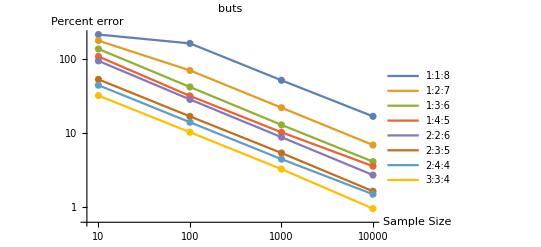

```mathematica
ListLogLogPlot[Transpose[Table[Table[{x,100*data[x][k]},{k,Keys[data[x]]}],{x,Keys[data]}]],PlotLegends->Keys[data[10]],Joined->True,Mesh->All,AxesLabel->{"Sample Size","Percent error"},PlotLabel -> "Average deviation of 5000 samples of different sizes"]
```

```mathematica
f[a_,k_,x_]:=a*x^k;
```

{a→3.76588,k→-0.539059}

```mathematica
res = Table[
fitData = Transpose[Table[Table[{x,data[x][k]},{k,Keys[data[x]]}],{x,Keys[data]}]][[i]];
(*Fit the function to the data*)fit=FindFit[fitData,{f[a,k,x]},{{a},{k}},x];
fit,{i,8}]
```

{{a→4.13806,k→-0.259526},{a→4.77526,k→-0.426748},{a→4.5006,k→-0.515162},{a→3.64751,k→-0.526746},{a→3.13612,k→-0.520644},{a→1.68303,k→-0.501002},{a→1.40139,k→-0.500746},{a→1.00814,k→-0.497974}}

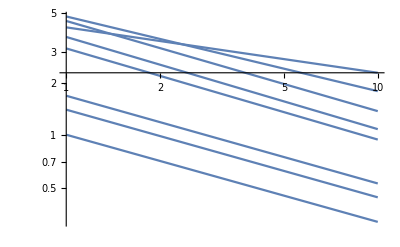

```mathematica
Show[Table[LogLogPlot[f[a,k,x]/.r,{x,1,10},PlotRange->All],{r,res}]]
```

```mathematica
Limit[f[a,k,x]/.res[[2]],{x->Infinity}]
```

0.